## 升压变换器设计_开环控制

现需要一种电路，输入低电压，输出高电压，boost电路是一种选择。

-Graphics-

### 1 需求分析

主电路参数
-Graphics-

根据需求可得:

```mathematica
(* Quit[] *) (*执行此命令以退出内核*);
```

```mathematica
Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]];
```

```mathematica
Subscript[V, INMIN] = 90;
Subscript[V, INMAX] = 110;
Subscript[V, OUT] = 400;
Subscript[I, OUT] = 5;
Subscript[η, L] = 0.2;
Subscript[η, C] = 0.01;
ΔI=Subscript[I, OUT] *Subscript[η, L] 
Subscript[ΔI, C] =Subscript[V, OUT] *Subscript[η, C] 
η = 0.95;
```

1.

4.

最恶劣工况：输入电压最低。此时，占空比最大,产生平均电流I_L=I_OUT/(1-D_MAX)最大。

```mathematica
Subscript[D, MAX]=(Subscript[V, OUT]-Subscript[V, INMIN])/Subscript[V, OUT] //N
```

0.775

```mathematica
Subscript[I, L] = Subscript[I, OUT]/(1-Subscript[D, MAX])
```

22.2222

根据电流纹波率，算出峰值电流

```mathematica
r= 0.2;
Subscript[I, PK]= Subscript[I, L] (1+ r/2)
```

24.4444

被控对象：Boost 电路

-Graphics-

### 2 开关频率选择

开关频率越高，电感尺寸越小，但损耗增加，效率下降。常见范围一般在20kHz至300kHz之间，平衡效率、尺寸和噪声。本文优先考虑效率，选取开关频率为16kHz。

```mathematica
fs = 16*^3;
```

### 3 电感选择

```mathematica
Subscript[V, ON]= 160;
L =ScientificForm[(Subscript[V, ON] *Subscript[D, MAX])/(r Subscript[I, L] fs) ]
```

1.74375×10^-3

### 4 输出电容选择

经验法则：额定纹波电流大于等于输出电容的最大有效值电流

```mathematica
Subscript[D, MAX]  = Subscript[D, MAX];
Subscript[r, DMAX] = r ;
Subscript[I, RMS_OUT] = Subscript[I, OUT] √((Subscript[D, MAX] + (Subscript[r, DMAX]^2/12))/(1 -Subscript[D, MAX]))
```

9.29954

输出电压纹波小于最大输出电压的20%
求得最小电容
https://blog.csdn.net/su165108515/article/details/131050567

```mathematica
Subscript[ΔV, OUT] = Subscript[V, OUT]  *0.2;
Subscript[C, MIN] = (Subscript[I, OUT] * Subscript[D, MAX])/(fs Subscript[ΔV, OUT])
```

3.02734×10^-6

### 5 输入电容选择

稳定输入电压

```mathematica
Subscript[ΔV, IN] = Subscript[V, INMIN]  *0.2;

Subscript[C, IN] =(ΔI Subscript[D, MAX])/(fs  Subscript[ΔV, IN])
```

2.69097×10^-6

### 6 PLECS仿真

开环仿真
-Graphics-
-Graphics-

### 7 控制器参数计算

过PLECS生产的Bode图，计算PI控制器参数

```mathematica
data=
Import["D:\code\28377d\hybrid-inverter-master\4_Sim\modules\lab2_boost\Boost双环PI控制\2_boost_i_loop_data.csv"];data=data⟦2;;⟧;
```

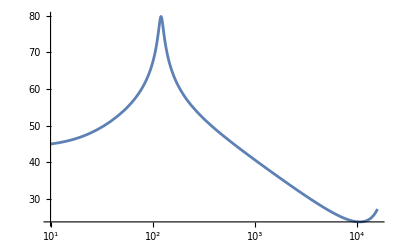

```mathematica
amp=Interpolation[data⟦;;,{1,2}⟧];
Plot[amp[f],{f,10,fs},ScalingFunctions->{"Log10",None}]
```

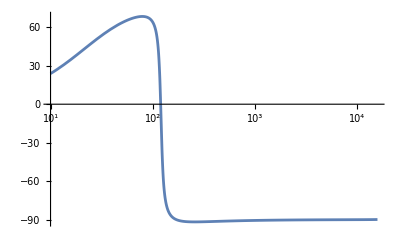

```mathematica
phase=Interpolation[data⟦;;,{1,3}⟧];
Plot[phase[f],{f,10,fs},ScalingFunctions->{"Log10",None}]
```

```mathematica
fc=fs/10//N
```

1600.

```mathematica
sol = FindRoot[{(20Log[10,Abs[(kp s+ ki)/s]]+amp[f] //.{s->ⅈ 2π f,f->fc}//ComplexExpand)==0,ki/(2Pi kp)== fc/10},{{kp,1},{ki,1}}]
```

{kp→0.014791,ki→14.8696}

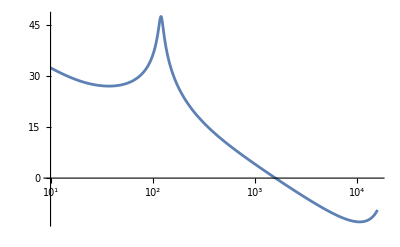

```mathematica
Plot[20Log[10,Abs[(kp s+ki)/s]]+amp[f] //.sol //.s->I 2Pi f //Evaluate,{f,10,fs},ScalingFunctions->{"Log10",None}]
```

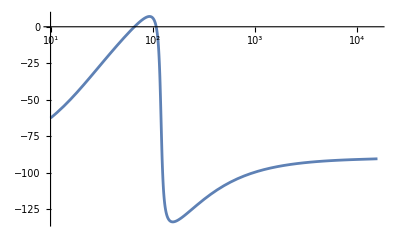

```mathematica
Plot[Arg[(kp s+ki)/s] 180/Pi+phase[f] //.sol //.s-> I  2 Pi f //Evaluate,{f,10,fs},ScalingFunctions->{"Log10",None}]
```

```mathematica
Manipulate[{LogLinearPlot[{20Log[10,Abs[(kp s+ki)/s]],20Log[10,Abs[(kp s+ki)/s]]+amp[f],amp[f],0}//.s->ⅈ 2π f//ComplexExpand//Evaluate,{f,10,fs},PlotRange->{-100,100},PlotLegends->{PI控制器,环路增益,被控对象}],LogLinearPlot[{Arg[(kp s+ki)/s] 180/π,Arg[(kp s+ki)/s] 180/π+phase[f],phase[f],-180}//.s->ⅈ 2π f//ComplexExpand//Evaluate,{f,10,fs},PlotRange->{-300,50},PlotLegends->{PI控制器,环路增益,被控对象}]},{kp,1*^-5,1*^-2},{ki,1*^-4,1*^2}]
```

微调最终系数
kp=0.014791
ki=14.8696

#### 8 闭环仿真测试

-Graphics-

### 参考文献

[1]Application Note 升压转换器功率级的基本计算 https://www.ti.com.cn/cn/lit/an/zhcabv1d/zhcabv1d.pdf?ts=1752409930275
[2]美 马尼克塔拉, 精通开关电源设计. 北京: 人民邮电出版社, 2008. 见于: 2025年6月14日. [在线]. 载于: https://www.zhangqiaokeyan.com/book-cn/081504538067.html
[3]Boost变换器单电压闭环PI控制+仿真验证  https://www.bilibili.com/video/BV1zz4y1h7Li/?spm_id_from=333.337.search-card.all.click&vd_source=f92eb336806a7a264c052ec82b31d75d